# ListDensityPlot de 1/100∫_0^100 𝔼[Tr[𝒟^2(t)] ]dt

```mathematica
SetDirectory[NotebookDirectory[]];
```

## XXZ L=7,d=4,J_z=1,ω=0, barriendo ε y J_xy de 0 a 2 (paso = 0.1)

```mathematica
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/xxz_w_defect_L_7_Jz_1_d_4_omega_0.csv"]]
```

{{\varepsilon,J_{xy},promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

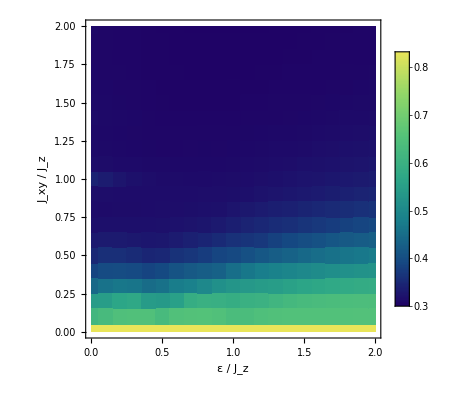

```mathematica
fontSize=22;

fig=ListDensityPlot[choiPurity,
ColorFunction->"BlueGreenYellow",
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"ε / J_z","J_xy / J_z"}
]
```

```mathematica
Export["tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_4.png",fig,"PNG"]
```

tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_4.png

## XXZ L=7,d=3,J_z=1,ω=0, barriendo ε y J_xy de 0 a 2 (paso = 0.1)

```mathematica
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/xxz_w_defect_L_7_Jz_1._d_3_omega_0..csv"]]
```

{{\varepsilon,J_{xy},promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

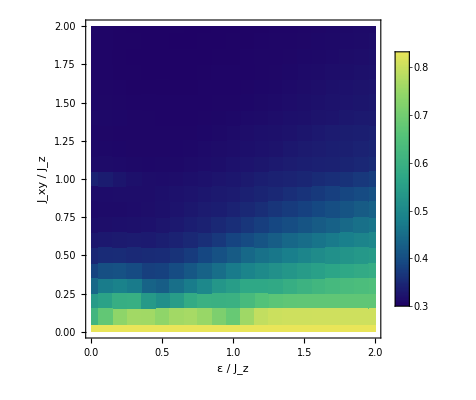

```mathematica
fontSize=22;

fig=ListDensityPlot[choiPurity,
ColorFunction->"BlueGreenYellow",
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"ε / J_z","J_xy / J_z"}
]
```

```mathematica
Export["tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_3.png",fig,"PNG"]
```

tmp/temporal_avg_haar_avg_choi_purity_xxz_L_7_Jz_1_omega_0_d_3.png

## XXZ L=7,d=3,J_z=1,ω=0, barriendo ε y J_xy de 0 a 2 (paso = 0.1)

```mathematica
(* Datos del promedio temporal del valor esperado de Haar de la pureza de Choi *)
{#[[1]],choiPurity=#[[2;;]];}&[Import["data/temporal_haar_avg_choi_purity/wisniacki_open_L_7_hx_1..csv"]]
```

{{hz,J,promedio temporal de 0 a 100 del valor esperado de Haar de la pureza de Choi},Null}

```mathematica
choiPurity=Flatten[Table[{Subdivide[0.,2.,20][[i]],Subdivide[0.,2.,20][[j]],choiPurity[[21*(i-1)+j,3]]},{i,21},{j,21}],1];
```

```mathematica
Select[Round[choiPurity,10.^-2],#[[1]]==2.00&&#[[2]]==0.0&]
```

{{2.,0.,1.}}

```mathematica
choiPurity
```

{{0.,0.,1.},{0.,0.1,0.458593},{0.,0.2,0.431874},{0.,0.3,0.422274},{0.,0.4,0.419401},{0.,0.5,0.416595},{0.,0.6,0.418229},{0.,0.7,0.409544},{0.,0.8,0.406992},{0.,0.9,0.405372},{0.,1.,0.39853},{0.,1.1,0.398736},{0.,1.2,0.396311},{0.,1.3,0.396029},{0.,1.4,0.400403},{0.,1.5,0.405631},{0.,1.6,0.410881},{0.,1.7,0.403173},{0.,1.8,0.421234},{0.,1.9,0.412925},{0.,2.,0.400865},{0.1,0.,1.},{0.1,0.1,0.457706},{0.1,0.2,0.429979},{0.1,0.3,0.417098},{0.1,0.4,0.406872},{0.1,0.5,0.362267},{0.1,0.6,0.330321},{0.1,0.7,0.306623},{0.1,0.8,0.303874},{0.1,0.9,0.294262},{0.1,1.,0.288871},{0.1,1.1,0.287455},{0.1,1.2,0.286153},{0.1,1.3,0.286253},{0.1,1.4,0.29081},{0.1,1.5,0.297972},{0.1,1.6,0.309761},{0.1,1.7,0.316724},{0.1,1.8,0.330149},{0.1,1.9,0.348377},{0.1,2.,0.368668},{0.2,0.,1.},{0.2,0.1,0.444893},{0.2,0.2,0.403361},{0.2,0.3,0.373073},{0.2,0.4,0.34939},{0.2,0.5,0.317659},{0.2,0.6,0.298533},{0.2,0.7,0.289609},{0.2,0.8,0.286195},{0.2,0.9,0.282874},{0.2,1.,0.280512},{0.2,1.1,0.278922},{0.2,1.2,0.278943},{0.2,1.3,0.281365},{0.2,1.4,0.286503},{0.2,1.5,0.293628},{0.2,1.6,0.304961},{0.2,1.7,0.318179},{0.2,1.8,0.332075},{0.2,1.9,0.352063},{0.2,2.,0.374231},{0.3,0.,1.},{0.3,0.1,0.409775},{0.3,0.2,0.360109},{0.3,0.3,0.334697},{0.3,0.4,0.318258},{0.3,0.5,0.302184},{0.3,0.6,0.292499},{0.3,0.7,0.286521},{0.3,0.8,0.282946},{0.3,0.9,0.280558},{0.3,1.,0.278878},{0.3,1.1,0.277993},{0.3,1.2,0.277784},{0.3,1.3,0.279094},{0.3,1.4,0.28229},{0.3,1.5,0.288188},{0.3,1.6,0.297726},{0.3,1.7,0.306791},{0.3,1.8,0.317753},{0.3,1.9,0.336538},{0.3,2.,0.357565},{0.4,0.,1.},{0.4,0.1,0.380423},{0.4,0.2,0.337706},{0.4,0.3,0.318802},{0.4,0.4,0.307783},{0.4,0.5,0.297741},{0.4,0.6,0.290643},{0.4,0.7,0.286073},{0.4,0.8,0.282624},{0.4,0.9,0.280206},{0.4,1.,0.27868},{0.4,1.1,0.278104},{0.4,1.2,0.277978},{0.4,1.3,0.278976},{0.4,1.4,0.280875},{0.4,1.5,0.28668},{0.4,1.6,0.29247},{0.4,1.7,0.29724},{0.4,1.8,0.306204},{0.4,1.9,0.321668},{0.4,2.,0.338797},{0.5,0.,1.},{0.5,0.1,0.376563},{0.5,0.2,0.332406},{0.5,0.3,0.314941},{0.5,0.4,0.304948},{0.5,0.5,0.297222},{0.5,0.6,0.290415},{0.5,0.7,0.286086},{0.5,0.8,0.283292},{0.5,0.9,0.281452},{0.5,1.,0.279481},{0.5,1.1,0.278997},{0.5,1.2,0.278772},{0.5,1.3,0.279552},{0.5,1.4,0.281193},{0.5,1.5,0.283586},{0.5,1.6,0.287374},{0.5,1.7,0.292437},{0.5,1.8,0.297976},{0.5,1.9,0.30846},{0.5,2.,0.316851},{0.6,0.,1.},{0.6,0.1,0.389915},{0.6,0.2,0.33615},{0.6,0.3,0.316568},{0.6,0.4,0.306197},{0.6,0.5,0.298048},{0.6,0.6,0.292138},{0.6,0.7,0.287677},{0.6,0.8,0.284859},{0.6,0.9,0.283339},{0.6,1.,0.281215},{0.6,1.1,0.280058},{0.6,1.2,0.279684},{0.6,1.3,0.280526},{0.6,1.4,0.281892},{0.6,1.5,0.283226},{0.6,1.6,0.285911},{0.6,1.7,0.291843},{0.6,1.8,0.294999},{0.6,1.9,0.302129},{0.6,2.,0.313592},{0.7,0.,1.},{0.7,0.1,0.405339},{0.7,0.2,0.343615},{0.7,0.3,0.318913},{0.7,0.4,0.307574},{0.7,0.5,0.300805},{0.7,0.6,0.294644},{0.7,0.7,0.290535},{0.7,0.8,0.287097},{0.7,0.9,0.285723},{0.7,1.,0.28345},{0.7,1.1,0.282397},{0.7,1.2,0.282774},{0.7,1.3,0.284488},{0.7,1.4,0.285613},{0.7,1.5,0.286555},{0.7,1.6,0.287618},{0.7,1.7,0.290154},{0.7,1.8,0.294825},{0.7,1.9,0.300646},{0.7,2.,0.307398},{0.8,0.,1.},{0.8,0.1,0.400066},{0.8,0.2,0.346333},{0.8,0.3,0.324003},{0.8,0.4,0.3123},{0.8,0.5,0.306492},{0.8,0.6,0.302144},{0.8,0.7,0.296376},{0.8,0.8,0.292597},{0.8,0.9,0.290496},{0.8,1.,0.287715},{0.8,1.1,0.28557},{0.8,1.2,0.285578},{0.8,1.3,0.285904},{0.8,1.4,0.287248},{0.8,1.5,0.289949},{0.8,1.6,0.292011},{0.8,1.7,0.295196},{0.8,1.8,0.297719},{0.8,1.9,0.301161},{0.8,2.,0.308506},{0.9,0.,1.},{0.9,0.1,0.410029},{0.9,0.2,0.356673},{0.9,0.3,0.336846},{0.9,0.4,0.324482},{0.9,0.5,0.31829},{0.9,0.6,0.310339},{0.9,0.7,0.303044},{0.9,0.8,0.298268},{0.9,0.9,0.295737},{0.9,1.,0.294528},{0.9,1.1,0.29293},{0.9,1.2,0.291796},{0.9,1.3,0.291916},{0.9,1.4,0.29079},{0.9,1.5,0.293076},{0.9,1.6,0.294373},{0.9,1.7,0.297259},{0.9,1.8,0.299032},{0.9,1.9,0.303594},{0.9,2.,0.313839},{1.,0.,1.},{1.,0.1,0.444052},{1.,0.2,0.379397},{1.,0.3,0.353838},{1.,0.4,0.341008},{1.,0.5,0.331146},{1.,0.6,0.322903},{1.,0.7,0.312923},{1.,0.8,0.307418},{1.,0.9,0.303951},{1.,1.,0.29851},{1.,1.1,0.297719},{1.,1.2,0.300857},{1.,1.3,0.30093},{1.,1.4,0.300007},{1.,1.5,0.30157},{1.,1.6,0.300764},{1.,1.7,0.301202},{1.,1.8,0.30578},{1.,1.9,0.306818},{1.,2.,0.313138},{1.1,0.,1.},{1.1,0.1,0.486024},{1.1,0.2,0.412607},{1.1,0.3,0.377524},{1.1,0.4,0.35945},{1.1,0.5,0.348554},{1.1,0.6,0.340269},{1.1,0.7,0.331049},{1.1,0.8,0.32032},{1.1,0.9,0.315836},{1.1,1.,0.307931},{1.1,1.1,0.30626},{1.1,1.2,0.306321},{1.1,1.3,0.30717},{1.1,1.4,0.310013},{1.1,1.5,0.308796},{1.1,1.6,0.307621},{1.1,1.7,0.309259},{1.1,1.8,0.311313},{1.1,1.9,0.312778},{1.1,2.,0.317314},{1.2,0.,1.},{1.2,0.1,0.525913},{1.2,0.2,0.452202},{1.2,0.3,0.411065},{1.2,0.4,0.384037},{1.2,0.5,0.366519},{1.2,0.6,0.355102},{1.2,0.7,0.34633},{1.2,0.8,0.332498},{1.2,0.9,0.3222},{1.2,1.,0.323802},{1.2,1.1,0.317957},{1.2,1.2,0.313758},{1.2,1.3,0.317453},{1.2,1.4,0.317817},{1.2,1.5,0.31907},{1.2,1.6,0.320224},{1.2,1.7,0.317516},{1.2,1.8,0.319549},{1.2,1.9,0.320628},{1.2,2.,0.324873},{1.3,0.,1.},{1.3,0.1,0.559317},{1.3,0.2,0.49155},{1.3,0.3,0.450546},{1.3,0.4,0.419742},{1.3,0.5,0.395014},{1.3,0.6,0.376123},{1.3,0.7,0.362498},{1.3,0.8,0.345482},{1.3,0.9,0.337407},{1.3,1.,0.330228},{1.3,1.1,0.328567},{1.3,1.2,0.326998},{1.3,1.3,0.324124},{1.3,1.4,0.325975},{1.3,1.5,0.326742},{1.3,1.6,0.329844},{1.3,1.7,0.331102},{1.3,1.8,0.331892},{1.3,1.9,0.335658},{1.3,2.,0.339179},{1.4,0.,1.},{1.4,0.1,0.587972},{1.4,0.2,0.5237},{1.4,0.3,0.487846},{1.4,0.4,0.45847},{1.4,0.5,0.432821},{1.4,0.6,0.405282},{1.4,0.7,0.387464},{1.4,0.8,0.368779},{1.4,0.9,0.354293},{1.4,1.,0.344377},{1.4,1.1,0.340808},{1.4,1.2,0.336444},{1.4,1.3,0.33294},{1.4,1.4,0.334537},{1.4,1.5,0.336841},{1.4,1.6,0.333761},{1.4,1.7,0.333199},{1.4,1.8,0.339686},{1.4,1.9,0.343417},{1.4,2.,0.349124},{1.5,0.,1.},{1.5,0.1,0.613352},{1.5,0.2,0.548908},{1.5,0.3,0.517211},{1.5,0.4,0.492805},{1.5,0.5,0.468351},{1.5,0.6,0.442918},{1.5,0.7,0.415522},{1.5,0.8,0.396623},{1.5,0.9,0.373088},{1.5,1.,0.362935},{1.5,1.1,0.348948},{1.5,1.2,0.346866},{1.5,1.3,0.347432},{1.5,1.4,0.344863},{1.5,1.5,0.345405},{1.5,1.6,0.344694},{1.5,1.7,0.340904},{1.5,1.8,0.347037},{1.5,1.9,0.343425},{1.5,2.,0.354529},{1.6,0.,1.},{1.6,0.1,0.63514},{1.6,0.2,0.568269},{1.6,0.3,0.539894},{1.6,0.4,0.518994},{1.6,0.5,0.499203},{1.6,0.6,0.477547},{1.6,0.7,0.443579},{1.6,0.8,0.421004},{1.6,0.9,0.399121},{1.6,1.,0.381186},{1.6,1.1,0.373849},{1.6,1.2,0.356988},{1.6,1.3,0.352998},{1.6,1.4,0.359115},{1.6,1.5,0.351281},{1.6,1.6,0.352275},{1.6,1.7,0.352727},{1.6,1.8,0.34746},{1.6,1.9,0.353494},{1.6,2.,0.357911},{1.7,0.,1.},{1.7,0.1,0.653888},{1.7,0.2,0.584498},{1.7,0.3,0.556672},{1.7,0.4,0.537432},{1.7,0.5,0.523118},{1.7,0.6,0.505578},{1.7,0.7,0.476191},{1.7,0.8,0.445016},{1.7,0.9,0.423866},{1.7,1.,0.403075},{1.7,1.1,0.389525},{1.7,1.2,0.379328},{1.7,1.3,0.370371},{1.7,1.4,0.36358},{1.7,1.5,0.364764},{1.7,1.6,0.354506},{1.7,1.7,0.359137},{1.7,1.8,0.358594},{1.7,1.9,0.356373},{1.7,2.,0.359074},{1.8,0.,1.},{1.8,0.1,0.670705},{1.8,0.2,0.598539},{1.8,0.3,0.569788},{1.8,0.4,0.551626},{1.8,0.5,0.540989},{1.8,0.6,0.525846},{1.8,0.7,0.501824},{1.8,0.8,0.474385},{1.8,0.9,0.4496},{1.8,1.,0.425095},{1.8,1.1,0.407027},{1.8,1.2,0.390589},{1.8,1.3,0.382802},{1.8,1.4,0.374624},{1.8,1.5,0.371823},{1.8,1.6,0.371138},{1.8,1.7,0.363042},{1.8,1.8,0.36688},{1.8,1.9,0.364805},{1.8,2.,0.362933},{1.9,0.,1.},{1.9,0.1,0.686323},{1.9,0.2,0.611034},{1.9,0.3,0.580699},{1.9,0.4,0.563538},{1.9,0.5,0.553615},{1.9,0.6,0.54025},{1.9,0.7,0.520469},{1.9,0.8,0.501125},{1.9,0.9,0.474004},{1.9,1.,0.450151},{1.9,1.1,0.428283},{1.9,1.2,0.407413},{1.9,1.3,0.399313},{1.9,1.4,0.392032},{1.9,1.5,0.384768},{1.9,1.6,0.378925},{1.9,1.7,0.37677},{1.9,1.8,0.370305},{1.9,1.9,0.375031},{1.9,2.,0.371145},{2.,0.,1.},{2.,0.1,0.700943},{2.,0.2,0.622776},{2.,0.3,0.590147},{2.,0.4,0.573536},{2.,0.5,0.563034},{2.,0.6,0.552015},{2.,0.7,0.533534},{2.,0.8,0.518021},{2.,0.9,0.500358},{2.,1.,0.471855},{2.,1.1,0.450814},{2.,1.2,0.42592},{2.,1.3,0.412727},{2.,1.4,0.405202},{2.,1.5,0.395042},{2.,1.6,0.392046},{2.,1.7,0.383758},{2.,1.8,0.38214},{2.,1.9,0.377137},{2.,2.,0.382847}}

```mathematica
Select[Round[choiPurity,10.^-2],#[[3]]>=0.7&]
```

{{0.,0.,1.},{0.1,0.,1.},{0.2,0.,1.},{0.3,0.,1.},{0.4,0.,1.},{0.5,0.,1.},{0.6,0.,1.},{0.7,0.,1.},{0.8,0.,1.},{0.9,0.,1.},{1.,0.,1.},{1.1,0.,1.},{1.2,0.,1.},{1.3,0.,1.},{1.4,0.,1.},{1.5,0.,1.},{1.6,0.,1.},{1.7,0.,1.},{1.8,0.,1.},{1.9,0.,1.},{2.,0.,1.},{2.,0.1,0.7}}

```mathematica
{Min[choiPurity[[;;,3]]],Select[Round[choiPurity,10.^-2],#[[3]]==0.28&]}
```

{0.277784,{{0.2,0.9,0.28},{0.2,1.,0.28},{0.2,1.1,0.28},{0.2,1.2,0.28},{0.2,1.3,0.28},{0.3,0.8,0.28},{0.3,0.9,0.28},{0.3,1.,0.28},{0.3,1.1,0.28},{0.3,1.2,0.28},{0.3,1.3,0.28},{0.3,1.4,0.28},{0.4,0.8,0.28},{0.4,0.9,0.28},{0.4,1.,0.28},{0.4,1.1,0.28},{0.4,1.2,0.28},{0.4,1.3,0.28},{0.4,1.4,0.28},{0.5,0.8,0.28},{0.5,0.9,0.28},{0.5,1.,0.28},{0.5,1.1,0.28},{0.5,1.2,0.28},{0.5,1.3,0.28},{0.5,1.4,0.28},{0.5,1.5,0.28},{0.6,0.8,0.28},{0.6,0.9,0.28},{0.6,1.,0.28},{0.6,1.1,0.28},{0.6,1.2,0.28},{0.6,1.3,0.28},{0.6,1.4,0.28},{0.6,1.5,0.28},{0.7,1.,0.28},{0.7,1.1,0.28},{0.7,1.2,0.28},{0.7,1.3,0.28}}}

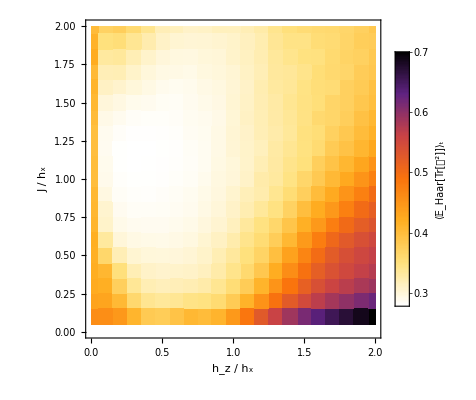

```mathematica
fontSize=22;

fig=ListDensityPlot[choiPurity,
ColorFunction->(ColorData["SunsetColors"][1-#]&),ColorFunctionScaling->True,
PlotRange->{0.25,0.75},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"}
]
```

```mathematica
Export["tmp/temporal_avg_haar_avg_choi_purity_wisniacki_open_L_7_hx_1.png",fig,"PNG"]
```

tmp/temporal_avg_haar_avg_choi_purity_wisniacki_open_L_7_hx_1.png